## Morse Potential

```mathematica
ClearAll["Global`*"]
```

Constants/Parameters

```mathematica
(*Constants (In Atomic Units)*)
m:=1
e:=1
ℏ:=1

k:=1    (*Force constant at the well minimum*)
De:=1    (*Well depth*)
re:=1    (*Equilibrium bond distance*)
a:=√(k/(2 De))

(*Parameters*)
R:=50
T:=100
fps:=60
numstates:=32
```

Definitions

```mathematica
(*Potential Energy*)
V[r_]:=De(Exp[-2 a(r-re)]-2 Exp[-a(r-re)])

(*Time Independent Schrodinger Equation*)
H=-ℏ^2/(2 m) ψ''[r]+V[r]*ψ[r];
```

Energy Eigenvalues/Eigenfunctions

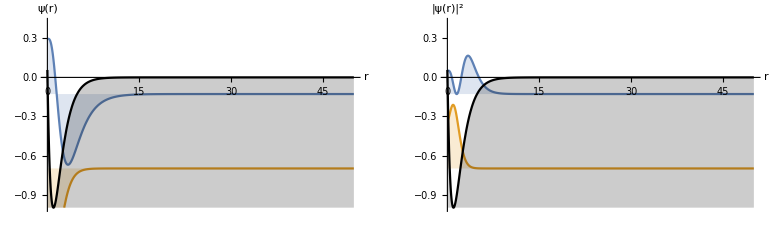

```mathematica
{vals,funs}=NDEigensystem[H,ψ[r],{r,0,R},numstates,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];

(*Since the potential tends to 0 too slowly, only use eigenvalues that are less than the value of the potential at the right boundary of the region to ensure we're getting bound states*)
boundindices:=Flatten[Position[vals,_?(#<V[R]&)]]
boundvals:=vals[[boundindices]]
boundfuns:=funs[[boundindices]]
numboundstates:=Length[boundvals]

upper:=Max[Map[FindMaxValue[{#,0≤r≤R},r]&,boundfuns]]
bounds:={-De,upper}

fillingrule:=Table[i->boundvals[[i]],{i,1,numboundstates}]
labels:=Table[ToString[Subscript[ψ, i],TraditionalForm],{i,1,numboundstates}]
title:=StringForm["Morse Potential: First `` Bound Stationary States",numboundstates]

GraphicsRow[{Show[Plot[Evaluate[boundfuns+boundvals],{r,0,R},AxesLabel->{"r","ψ(r)"},Filling->fillingrule,PlotRange->bounds],Plot[V[r],{r,0,R},Filling->Bottom,PlotStyle->Black,PlotRange->bounds]],Show[Plot[Evaluate[boundfuns^2+boundvals],{r,0,R},AxesLabel->{"r","|ψ(r)|^2"},Filling->fillingrule,PlotRange->bounds],Plot[V[r],{r,0,R},Filling->Bottom,PlotStyle->Black,PlotRange->bounds]]},PlotLabel->title,ImageSize->Large]
```

Stationary States

```mathematica
ϵn[n_]:=Part[boundvals,n];
ψn[n_]:=Part[boundfuns,n];
Ψn[n_]:=ψn[n] Exp[-ℏ ϵn[n] t/I];
```

Mixed State

```mathematica
ψ=ψn[1];
Ψ=Ψn[1];

norm=Sqrt[NIntegrate[(Conjugate[ψ] ψ),{r,0,R}]];
Ψ=Ψ/norm;
```

```mathematica
animation:=Animate[Show[Plot[Evaluate[Conjugate[Ψ] Ψ]+(ϵn[1]+ϵn[3]+ϵn[4])/.t->s,{r,0,R},Axes->True,AxesLabel->{"r","|ψ(r)|^2"},PlotRange->bounds,PlotStyle->Red],Plot[V[r],{r,0,R},Filling->Axis,PlotStyle->Black,Exclusions->None]],{s,0,T},DisplayAllSteps->True,DefaultDuration->T,AnimationRunning->False];
animation
```